## Differences between primes

```mathematica
Get[StringJoin[NotebookDirectory[] , "nprimes.mx"]]
```

```mathematica
primes=Table[Prime[x]^(15-1), {x,10000}];
```

```mathematica
results={};
```

## Prime 13

```mathematica
diffs = Table[primes[[n+1]]-primes[[n]],{n,Length@primes-1}];
series=Table[{x,diffs[[x]]},{x,Length@diffs}];
```

## Visibility Graph

```mathematica
natLinks =naturalVisibility[series];
```

## Graph

```mathematica
igv13=Graph[natLinks, DirectedEdges->False, VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igv13];
```

```mathematica
count = Total[adj]//Counts
```

<|269→9,177→6,179→6,268→7,416→1,470→1,267→5,476→1,494→2,492→1,485→1,265→1,507→1,550→1,556→1,531→1,270→1,570→1,484→1,566→1,546→1,271→2,588→1,273→2,581→1,584→1,274→2,603→1,266→2,609→1,578→1,623→2,278→3,276→1,649→1,282→1,283→1,644→1,264→1,279→1,281→2,617→1,290→3,660→1,289→2,690→1,286→1,291→1,297→2,704→1,300→1,683→1,304→1,280→1,727→1,305→1,312→1,307→1,316→1,709→1,217→5,320→1,748→1,315→2,318→2,319→2,759→1,335→1,331→1,336→1,334→1,764→1,347→1,342→1,343→1,309→1,337→1,768→1,338→1,359→1,371→1,346→1,373→1,786→1,403→1,808→1,311→1,339→1,365→1,396→1,801→1,412→1,425→1,411→1,851→1,432→1,455→1,364→1,445→1,443→2,861→1,192→7,818→1,911→1,366→1,921→1,429→1,916→1,943→1,974→1,992→1,923→1,968→1,984→1,1071→1,1078→1,1076→1,1079→1,1123→1,1120→1,1105→1,1143→1,1188→1,1212→1,1270→1,1216→1,1238→1,1156→1,1237→1,1314→1,1312→1,1356→1,1285→1,1322→1,1341→1,1378→1,1515→1,1516→1,893→1,1559→1,1542→1,1562→1,1605→1,1658→1,1652→1,1722→1,1812→1,1814→1,1813→1,1871→1,1869→1,1922→1,1908→1,1910→1,1911→1,1933→1,2001→2,2074→1,2163→1,2150→1,2156→1,2159→1,2310→1,2261→1,2320→1,2399→1,2643→1,2747→1,2767→1,1612→1,2661→1,2855→1,2809→1,2862→1,2909→1,3043→1,3066→1,2969→1,3241→1,3275→1,3311→1,1299→1,3267→1,3486→1,3476→1,3559→1,3585→1,3613→1,3579→1,3628→1,3649→1,3565→1,3652→1,3822→1,3808→1,3869→1,3910→1,4101→1,4095→1,3997→1,4121→1,4138→1,4182→1,4211→1,4244→1,4264→1,4207→1,4226→1,4359→1,4402→1,4462→1,4567→1,975→1,4552→1,4556→1,4232→1,4633→1,4764→1,4900→1,2773→1,4877→1,4953→1,4955→1,5210→1,5300→1,4982→1,5493→1,5473→1,5756→1,4467→1,5655→1,5910→1,5804→1,5292→1,6204→1,6360→1,173→9,185→8,182→5,181→8,180→7,170→14,258→1,169→9,176→8,254→1,183→12,178→6,186→3,251→1,248→1,245→2,242→1,175→5,238→3,239→1,167→13,172→4,236→2,237→1,233→1,235→2,231→2,171→8,232→1,230→1,164→7,226→2,161→8,168→7,224→2,223→1,222→3,225→3,165→5,220→2,163→9,158→5,218→4,219→2,166→5,162→8,157→8,216→2,215→2,208→6,212→3,211→1,214→2,204→2,155→12,209→1,207→5,160→3,201→3,203→1,154→12,205→2,202→1,196→8,156→12,149→10,199→2,197→5,198→4,150→15,194→8,193→3,152→11,151→12,195→3,191→3,190→8,148→10,189→6,187→9,146→20,159→3,153→10,188→4,184→7,144→9,147→4,145→9,143→18,142→23,140→14,141→13,174→2,139→13,120→18,132→19,131→14,124→18,119→16,122→13,134→13,129→12,121→20,133→14,138→16,137→18,128→15,125→19,135→27,126→13,136→20,127→16,116→25,118→19,123→6,117→14,114→23,130→7,115→19,108→25,111→19,110→15,113→10,112→15,109→18,101→37,105→21,107→24,102→37,103→22,90→25,99→28,97→30,92→35,106→24,94→28,93→26,104→15,91→34,100→28,98→20,95→41,88→22,96→31,89→28,87→22,83→30,82→30,85→29,81→44,79→46,86→20,77→50,80→46,84→20,78→43,70→86,76→43,73→57,74→64,71→90,75→54,69→72,72→58,68→39,62→58,64→35,66→34,67→38,65→33,61→64,63→62,59→50,60→49,58→58,57→55,56→51,53→51,55→32,52→40,49→31,50→28,43→61,48→30,41→54,54→56,47→50,51→26,42→43,44→44,45→34,46→30,39→42,40→62,37→33,35→34,30→33,36→32,28→53,33→30,20→95,34→39,38→22,26→44,32→31,31→33,27→54,29→41,23→60,19→75,25→48,21→77,22→81,24→56,16→108,17→79,18→72,13→127,12→146,15→119,14→136,11→161,9→220,10→184,4→682,7→310,8→239,5→523,6→381,3→866,2→510|>

```mathematica
count[1]=.
```

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{269,1/1111},{177,2/3333},{179,2/3333},{268,7/9999},{416,1/9999},{470,1/9999},{267,5/9999},{476,1/9999},{494,2/9999},{492,1/9999},{485,1/9999},{265,1/9999},{507,1/9999},{550,1/9999},{556,1/9999},{531,1/9999},{270,1/9999},{570,1/9999},{484,1/9999},{566,1/9999},{546,1/9999},{271,2/9999},{588,1/9999},{273,2/9999},{581,1/9999},{584,1/9999},{274,2/9999},{603,1/9999},{266,2/9999},{609,1/9999},{578,1/9999},{623,2/9999},{278,1/3333},{276,1/9999},{649,1/9999},{282,1/9999},{283,1/9999},{644,1/9999},{264,1/9999},{279,1/9999},{281,2/9999},{617,1/9999},{290,1/3333},{660,1/9999},{289,2/9999},{690,1/9999},{286,1/9999},{291,1/9999},{297,2/9999},{704,1/9999},{300,1/9999},{683,1/9999},{304,1/9999},{280,1/9999},{727,1/9999},{305,1/9999},{312,1/9999},{307,1/9999},{316,1/9999},{709,1/9999},{217,5/9999},{320,1/9999},{748,1/9999},{315,2/9999},{318,2/9999},{319,2/9999},{759,1/9999},{335,1/9999},{331,1/9999},{336,1/9999},{334,1/9999},{764,1/9999},{347,1/9999},{342,1/9999},{343,1/9999},{309,1/9999},{337,1/9999},{768,1/9999},{338,1/9999},{359,1/9999},{371,1/9999},{346,1/9999},{373,1/9999},{786,1/9999},{403,1/9999},{808,1/9999},{311,1/9999},{339,1/9999},{365,1/9999},{396,1/9999},{801,1/9999},{412,1/9999},{425,1/9999},{411,1/9999},{851,1/9999},{432,1/9999},{455,1/9999},{364,1/9999},{445,1/9999},{443,2/9999},{861,1/9999},{192,7/9999},{818,1/9999},{911,1/9999},{366,1/9999},{921,1/9999},{429,1/9999},{916,1/9999},{943,1/9999},{974,1/9999},{992,1/9999},{923,1/9999},{968,1/9999},{984,1/9999},{1071,1/9999},{1078,1/9999},{1076,1/9999},{1079,1/9999},{1123,1/9999},{1120,1/9999},{1105,1/9999},{1143,1/9999},{1188,1/9999},{1212,1/9999},{1270,1/9999},{1216,1/9999},{1238,1/9999},{1156,1/9999},{1237,1/9999},{1314,1/9999},{1312,1/9999},{1356,1/9999},{1285,1/9999},{1322,1/9999},{1341,1/9999},{1378,1/9999},{1515,1/9999},{1516,1/9999},{893,1/9999},{1559,1/9999},{1542,1/9999},{1562,1/9999},{1605,1/9999},{1658,1/9999},{1652,1/9999},{1722,1/9999},{1812,1/9999},{1814,1/9999},{1813,1/9999},{1871,1/9999},{1869,1/9999},{1922,1/9999},{1908,1/9999},{1910,1/9999},{1911,1/9999},{1933,1/9999},{2001,2/9999},{2074,1/9999},{2163,1/9999},{2150,1/9999},{2156,1/9999},{2159,1/9999},{2310,1/9999},{2261,1/9999},{2320,1/9999},{2399,1/9999},{2643,1/9999},{2747,1/9999},{2767,1/9999},{1612,1/9999},{2661,1/9999},{2855,1/9999},{2809,1/9999},{2862,1/9999},{2909,1/9999},{3043,1/9999},{3066,1/9999},{2969,1/9999},{3241,1/9999},{3275,1/9999},{3311,1/9999},{1299,1/9999},{3267,1/9999},{3486,1/9999},{3476,1/9999},{3559,1/9999},{3585,1/9999},{3613,1/9999},{3579,1/9999},{3628,1/9999},{3649,1/9999},{3565,1/9999},{3652,1/9999},{3822,1/9999},{3808,1/9999},{3869,1/9999},{3910,1/9999},{4101,1/9999},{4095,1/9999},{3997,1/9999},{4121,1/9999},{4138,1/9999},{4182,1/9999},{4211,1/9999},{4244,1/9999},{4264,1/9999},{4207,1/9999},{4226,1/9999},{4359,1/9999},{4402,1/9999},{4462,1/9999},{4567,1/9999},{975,1/9999},{4552,1/9999},{4556,1/9999},{4232,1/9999},{4633,1/9999},{4764,1/9999},{4900,1/9999},{2773,1/9999},{4877,1/9999},{4953,1/9999},{4955,1/9999},{5210,1/9999},{5300,1/9999},{4982,1/9999},{5493,1/9999},{5473,1/9999},{5756,1/9999},{4467,1/9999},{5655,1/9999},{5910,1/9999},{5804,1/9999},{5292,1/9999},{6204,1/9999},{6360,1/9999},{173,1/1111},{185,8/9999},{182,5/9999},{181,8/9999},{180,7/9999},{170,14/9999},{258,1/9999},{169,1/1111},{176,8/9999},{254,1/9999},{183,4/3333},{178,2/3333},{186,1/3333},{251,1/9999},{248,1/9999},{245,2/9999},{242,1/9999},{175,5/9999},{238,1/3333},{239,1/9999},{167,13/9999},{172,4/9999},{236,2/9999},{237,1/9999},{233,1/9999},{235,2/9999},{231,2/9999},{171,8/9999},{232,1/9999},{230,1/9999},{164,7/9999},{226,2/9999},{161,8/9999},{168,7/9999},{224,2/9999},{223,1/9999},{222,1/3333},{225,1/3333},{165,5/9999},{220,2/9999},{163,1/1111},{158,5/9999},{218,4/9999},{219,2/9999},{166,5/9999},{162,8/9999},{157,8/9999},{216,2/9999},{215,2/9999},{208,2/3333},{212,1/3333},{211,1/9999},{214,2/9999},{204,2/9999},{155,4/3333},{209,1/9999},{207,5/9999},{160,1/3333},{201,1/3333},{203,1/9999},{154,4/3333},{205,2/9999},{202,1/9999},{196,8/9999},{156,4/3333},{149,10/9999},{199,2/9999},{197,5/9999},{198,4/9999},{150,5/3333},{194,8/9999},{193,1/3333},{152,1/909},{151,4/3333},{195,1/3333},{191,1/3333},{190,8/9999},{148,10/9999},{189,2/3333},{187,1/1111},{146,20/9999},{159,1/3333},{153,10/9999},{188,4/9999},{184,7/9999},{144,1/1111},{147,4/9999},{145,1/1111},{143,2/1111},{142,23/9999},{140,14/9999},{141,13/9999},{174,2/9999},{139,13/9999},{120,2/1111},{132,19/9999},{131,14/9999},{124,2/1111},{119,16/9999},{122,13/9999},{134,13/9999},{129,4/3333},{121,20/9999},{133,14/9999},{138,16/9999},{137,2/1111},{128,5/3333},{125,19/9999},{135,3/1111},{126,13/9999},{136,20/9999},{127,16/9999},{116,25/9999},{118,19/9999},{123,2/3333},{117,14/9999},{114,23/9999},{130,7/9999},{115,19/9999},{108,25/9999},{111,19/9999},{110,5/3333},{113,10/9999},{112,5/3333},{109,2/1111},{101,37/9999},{105,7/3333},{107,8/3333},{102,37/9999},{103,2/909},{90,25/9999},{99,28/9999},{97,10/3333},{92,35/9999},{106,8/3333},{94,28/9999},{93,26/9999},{104,5/3333},{91,34/9999},{100,28/9999},{98,20/9999},{95,41/9999},{88,2/909},{96,31/9999},{89,28/9999},{87,2/909},{83,10/3333},{82,10/3333},{85,29/9999},{81,4/909},{79,46/9999},{86,20/9999},{77,50/9999},{80,46/9999},{84,20/9999},{78,43/9999},{70,86/9999},{76,43/9999},{73,19/3333},{74,64/9999},{71,10/1111},{75,6/1111},{69,8/1111},{72,58/9999},{68,13/3333},{62,58/9999},{64,35/9999},{66,34/9999},{67,38/9999},{65,1/303},{61,64/9999},{63,62/9999},{59,50/9999},{60,49/9999},{58,58/9999},{57,5/909},{56,17/3333},{53,17/3333},{55,32/9999},{52,40/9999},{49,31/9999},{50,28/9999},{43,61/9999},{48,10/3333},{41,6/1111},{54,56/9999},{47,50/9999},{51,26/9999},{42,43/9999},{44,4/909},{45,34/9999},{46,10/3333},{39,14/3333},{40,62/9999},{37,1/303},{35,34/9999},{30,1/303},{36,32/9999},{28,53/9999},{33,10/3333},{20,95/9999},{34,13/3333},{38,2/909},{26,4/909},{32,31/9999},{31,1/303},{27,6/1111},{29,41/9999},{23,20/3333},{19,25/3333},{25,16/3333},{21,7/909},{22,9/1111},{24,56/9999},{16,12/1111},{17,79/9999},{18,8/1111},{13,127/9999},{12,146/9999},{15,119/9999},{14,136/9999},{11,161/9999},{9,20/909},{10,184/9999},{4,62/909},{7,310/9999},{8,239/9999},{5,523/9999},{6,127/3333},{3,866/9999},{2,170/3333}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[0.156407/x^0.900917]

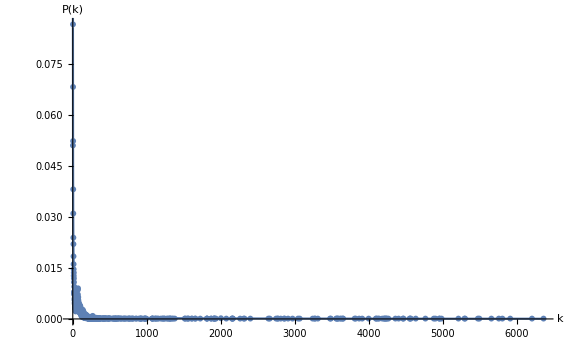

```mathematica
vis13=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"v-11.eps",vis11];
```

## Mean degree

```mathematica
degree=VertexDegree[igv13]//Mean//N
```

84.4072

## Record result

```mathematica
AppendTo[results, Flatten[{"visibility", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Horizontal Visibility Graph

```mathematica
horLinks=horizontalVisibility[series];
```

## Graph

```mathematica
igh13=Graph[horLinks, VertexLabels->"Name",DirectedEdges->False,VertexLabelStyle-> Large,GraphLayout->"CircularEmbedding"];
```

```mathematica
adj=AdjacencyMatrix[igh13];
```

```mathematica
count = Total[adj]//Counts
```

<|1→1,2→3364,5→934,4→1552,6→646,3→2227,9→193,7→426,8→284,10→145,11→84,12→67,13→36,15→13,14→19,16→3,19→1,18→1,20→1,22→1,17→1|>

```mathematica
count[1]=.
```

```mathematica
countrel = Table[{x,Lookup[count,x]/Length@diffs}, {x,Keys[count]}]
```

{{2,3364/9999},{5,934/9999},{4,1552/9999},{6,646/9999},{3,2227/9999},{9,193/9999},{7,142/3333},{8,284/9999},{10,145/9999},{11,28/3333},{12,67/9999},{13,4/1111},{15,13/9999},{14,19/9999},{16,1/3333},{19,1/9999},{18,1/9999},{20,1/9999},{22,1/9999},{17,1/9999}}

## Model fit

```mathematica
nlm=NonlinearModelFit[countrel,b x^-a,{a,b},x]
```

FittedModel[1.0749/x^1.58422]

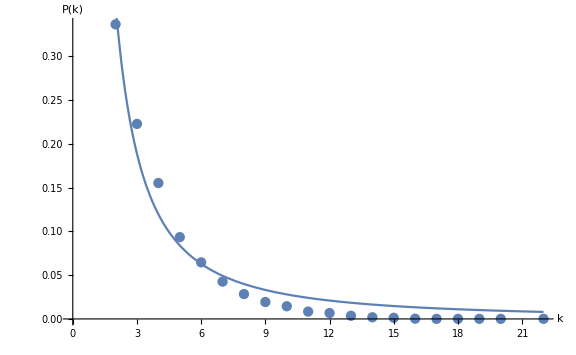

```mathematica
hvis13=Show[
ListPlot[countrel,PlotRange->All,AxesOrigin->{0,0}],Plot[nlm[x],{x,0,Max[Keys[count]]},PlotRange->All,AxesOrigin->{0,0}],
AxesLabel-> {Style["k",38, Italic],Style["P(k)", 38,Italic]},LabelStyle->Large,ImageSize->Large
]
```

```mathematica
Export[NotebookDirectory[]<>"hv-11.eps",hvis11];
```

## Mean degree

```mathematica
degree=VertexDegree[igh13]//Mean//N
```

3.94099

## Record result

```mathematica
AppendTo[results, Flatten[{"horizontal", ToString@n,Length@diffs, degree,ToString@#1<>" ± "<>ToString[Differences[#2][[1]]/2]&@@@nlm["ParameterConfidenceIntervalTableEntries"][[All,{1,3}]]}]];
```

## Return result

```mathematica
results
```

{{visibility,13,9999,84.4072,0.900917 ± 0.0341217,0.156407 ± 0.0103017},{horizontal,13,9999,3.94099,1.58422 ± 0.199777,1.0749 ± 0.219246}}